# Catenoide y helicoide

### Curvas y funciones definidas por Gray

```mathematica
cissoid[a_][t_] := 2 a {t^2, t^3}/(1 + t^2)
tractrix[a_][t_] := a {Sin[t], Cos[t] + Log[Tan[t/2]]}
catenary[a_][t_] := {a Cosh[t/a], t}
cardioid[a_][t_] := 2 a (1 + Cos[t]) {Cos[t], Sin[t]}
logspiral[a_, b_][t_] := a {Exp[b t] Cos[t], Exp[b t] Sin[t]}
cycloid[a_, b_][t_] := {a t - b Sin[t], a - b Cos[t]}

sphericalloxodrome[a_,b_][t_]:={2a Exp[b t]Cos[t],2a Exp[b t]Sin[t],-1+a^2 Exp[2b t]}/(1+a^2 Exp[2b t])

tx[A_, v_, o_ : {0, 0}] := Text[FontForm[A, {"Helvetica", 18}], v, o]

parabola[a_][t_] := {2 a t, t^2}
ellipse[a_, b_][t_] := {a Cos[t], b Sin[t]}
circ[a_] := ellipse[a, a]

Unprotect[L]; L[v_] := Sqrt[Simplify[v . v]]; Protect[L]; (*Norma*)
Unprotect[J]; J[{x_, y_}] := {-y, x}; Protect[J];(*Ortogonal*)

κ2[α_][t_] := α''[tt] . J[α'[tt]]/L[α'[tt]]^3 /. tt -> t (*Curvatura*)

arclength[α_] := Integrate[L[α'[tt]], tt] /. tt -> t
length[a_, b_][α_] := Integrate[L[α'[tt]], {tt, a, b}, GenerateConditions -> False]

lengthn[a_, b_][α_] := Module[{t}, NIntegrate[L[α'[t]], {t, a, b}]];
```

## Catenoide

Primero construimos la catenoide como superficie de revolución usando el código de la vez pasada:

```mathematica
(*Definamos una curva en el plano yz*)
γ[t_]:={0,Cosh[t], t}
G1:=ParametricPlot3D[γ[t],{t,-1,1}]
(*Para rotar, definamos la matriz*)
R[θ_]:=RotationMatrix[θ,{0,0,1}]
X[u_,v_]:=R[u].γ[v]
StringForm["La parametrización es X(u,v)=``",X[u,v]]
G2=ParametricPlot3D[X[u,v],{u,0,2Pi},{v,-1,1},Boxed->False,Axes->False]
```

La parametrización es X(u,v)={-Cosh[v] Sin[u],Cos[u] Cosh[v],v}

-Graphics3D-

### Curvas en la helicoide

SetDelayed::write: Tag Times in π/4[t_] is Protected.

$Failed

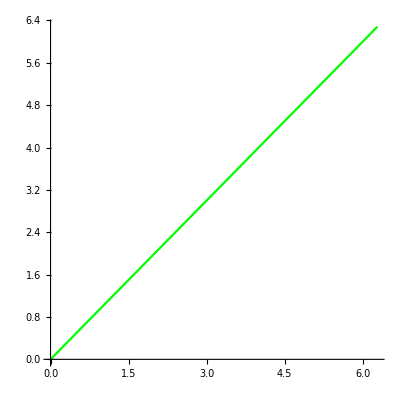
{-Graphics-,-Graphics3D-}

```mathematica
(*Definamos una curva β en el dominio de la parametrización*)
β[t_]:={t,t}
(*Y la levantamos a la superficie componiendo con la parametrización*)
α[t_]:=X[β[t][[1]],β[t][[2]]]

G3:=ParametricPlot[β[t],{t,0,2Pi},PlotStyle->{Green}](*Gráfica de la curva en R2*)
G4:=ParametricPlot3D[α[t],{t,-1,1},PlotStyle->{Green}] (*Gráfica de la curva en la superficie*)

{G3,Show[G2,G4,Boxed->False,Axes->False,PlotRange->All,ImageSize->Medium]}
```

### Primera forma fundamental

```mathematica
(*El siguiente paso es calcular la primera forma fundamental*)
Xu:=D[X[u,v],u]
Xv:=D[X[u,v],v]
A:=Xu.Xu
F:=Xu.Xv
G:=Xv.Xv

(*Formateamos el output para poder leerlo*)
Print[Column[{,StringForm["``=``",Subscript[X,u],Xu],StringForm["``=``",Subscript[X,v],Xv],StringForm["E=<``,``>=``",Subscript[X,u],Subscript[X,u],Simplify[A]],StringForm["F=<``,``>=``",Subscript[X,u],Subscript[X,v],Simplify[F]],StringForm["G=<``,``>=``",Subscript[X,v],Subscript[X,v],Simplify[G]]}]]

(*Aquí simplemente definimos las funciones que evaluan la primera forma fundamental sobre la curva β*)
A1:=A/.{u->β[t][[1]],v->β[t][[2]]}
F1:=F/.{u->β[t][[1]],v->β[t][[2]]}
G1:=G/.{u->β[t][[1]],v->β[t][[2]]}

(*La longitud de la curva α ya en la superficie*)
Long[β_]:=Integrate[Sqrt[A1*β'[t][[1]]+2*F1*β'[t][[1]]β'[t][[2]]+G1*β'[t][[2]]],{t,0,2Pi}]
StringForm["Long(α)= ``",Long[β]]
```

X_u={-Cos[u] Cosh[v],-Cosh[v] Sin[u],0}
X_v={-Sin[u] Sinh[v],Cos[u] Sinh[v],1}
E=<X_u,X_u>=Cosh[v]^2
F=<X_u,X_v>=0
G=<X_v,X_v>=Cosh[v]^2

Long(α)= √2 Sinh[2 π]

### Vectores y plano tangente

```mathematica
(*Dibujamos los vectores tangentes Xu y Xv y el plano tangente en un punto P del dominio*)
P:={0,1}
Yu:=Xu/.{u->P[[1]],v->P[[2]]}
Yv:=Xv/.{u->P[[1]],v->P[[2]]}
Tu:=Graphics3D[{Red,Thick, Arrow[{X[P[[1]],P[[2]]],X[P[[1]],P[[2]]]+Yu}]}]
Tv:=Graphics3D[{Red,Thick,Arrow[{X[P[[1]],P[[2]]],X[P[[1]],P[[2]]]+Yv}]}]
P1:=ParametricPlot3D[X[P[[1]],P[[2]]]+a*Yu+b*Yv,{a,-1,1},{b,-1,1},PlotStyle->{Blue,Opacity[0.5]}]
Show[G2,Tu,Tv,P1,PlotRange->All]
```

-Graphics3D-

```mathematica
(*Para medir áreas*)
(*R:=ParametricRegion[{s,t},{{s,0,2π},{t,0,2π}}]
RegionPlot[R]*)
(*Integrate[Sqrt[(A/.{u->x,v->y})(G/.{u->x,v->y})-(F/.{u->x,v->y})^2],Element[{x,y},R]]*)
```

## Helicoide

Y ahora construimos la helicoide usando la parametrización natural. Calculamos su primera forma fundamental:

```mathematica
Y[u_,v_]:={v*Cos[u],v*Sin[u],u}
H=ParametricPlot3D[Y[u,v],{u,0,2π},{v,-1,1},PlotStyle->{Green},Axes->False,Boxed->False]
(*El siguiente paso es calcular la primera forma fundamental*)
Yu:=D[Y[u,v],u]
Yv:=D[Y[u,v],v]

Ay:=Yu.Yu
Fy:=Yu.Yv
Gy:=Yv.Yv

(*Formateamos el output para poder leerlo*)
Print[Column[{,StringForm["``=``",Subscript[Y,u],Yu],StringForm["``=``",Subscript[Y,v],Yv],StringForm["E=<``,``>=``",Subscript[Y,u],Subscript[Y,u],Ay],StringForm["F=<``,``>=``",Subscript[Y,u],Subscript[Y,v],Fy],StringForm["G=<``,``>=``",Subscript[Y,v],Subscript[Y,v],Gy]}]]
```

-Graphics3D-

Y_u={-v Sin[u],v Cos[u],1}
Y_v={Cos[u],Sin[u],0}
E=<Y_u,Y_u>=1+v^2 Cos[u]^2+v^2 Sin[u]^2
F=<Y_u,Y_v>=0
G=<Y_v,Y_v>=Cos[u]^2+Sin[u]^2

Comparemos las formas fundamentales de las dos superficies. ¡No son iguales!

```mathematica
Simplify[Ay]==Simplify[A]
Simplify[Fy]==Simplify[F]
Simplify[Gy]==Simplify[G]
```

1+v^2==Cosh[v]^2

True

1==Cosh[v]^2

Para arreglarlo, tomemos el cambio de variable u*=u, v*=senh(v), (esta función de cambio de variable es diferenciable e invertible). Obtenemos esta nueva parametrización:

```mathematica
Y[u_,v_]:={Sinh[v]*Cos[u],Sinh[v]*Sin[u],u}
H=ParametricPlot3D[Y[u,v],{u,0,2π},{v,-1,1},PlotStyle->{Green},Axes->False,Boxed->False]
(*El siguiente paso es calcular la primera forma fundamental*)
Yu:=D[Y[u,v],u]
Yv:=D[Y[u,v],v]

Ay:=Yu.Yu
Fy:=Yu.Yv
Gy:=Yv.Yv

(*Formateamos el output para poder leerlo*)
Print[Column[{,StringForm["``=``",Subscript[Y,u],Yu],StringForm["``=``",Subscript[Y,v],Yv],StringForm["E=<``,``>=``",Subscript[Y,u],Subscript[Y,u],Ay],StringForm["F=<``,``>=``",Subscript[Y,u],Subscript[Y,v],Fy],StringForm["G=<``,``>=``",Subscript[Y,v],Subscript[Y,v],Gy]}]]
```

-Graphics3D-

Y_u={-Sin[u] Sinh[v],Cos[u] Sinh[v],1}
Y_v={Cos[u] Cosh[v],Cosh[v] Sin[u],0}
E=<Y_u,Y_u>=1+Cos[u]^2 Sinh[v]^2+Sin[u]^2 Sinh[v]^2
F=<Y_u,Y_v>=0
G=<Y_v,Y_v>=Cos[u]^2 Cosh[v]^2+Cosh[v]^2 Sin[u]^2

Comparemos las formas fundamentales:

```mathematica
Simplify[Ay]==Simplify[A]
Simplify[Fy]==Simplify[F]
Simplify[Gy]==Simplify[G]
```

True

True

True

```mathematica
Manipulate[ParametricPlot3D[t*X[u,v]+(1-t)*Y[u,v],{u,0,2π},{v,-1,1},Boxed->False,Axes->False,ColorFunction->"Rainbow"],{t,0,1}]
```